```mathematica
zero={{0,0},{0,0}};
```

```mathematica
Σ=ArrayFlatten[{{ⅈ PauliMatrix[2],zero},{zero,ⅈ PauliMatrix[2]}}];
```

(A | Cc
Cc | B)

```mathematica
s=Table[RandomReal[{1,10}],{i,10^2}];
d=Table[RandomReal[{1-s[[i]],s[[i]]-1}],{i,10^2}];
g=Table[RandomReal[{2 Abs[d[[i]]]+1,100}],{i,10^2}];
λ=Table[RandomReal[{-1,1}],{i,10^2}];

a=Table[s[[i]]+d[[i]],{i,10^2}];
Length[a];
b=Table[s[[i]]-d[[i]],{i,10^2}];
Length[b];

cp=Table[
1/(4 √(s[[i]]^2-d[[i]]^2))*(√((4 d[[i]]^2+1/2(g[[i]]^2+1)(λ[[i]]-1)-(2 d[[i]]^2+g[[i]])(λ[[i]]+1))^2-4 g[[i]]^2)+√((4 s[[i]]^2+1/2(g[[i]]^2+1)(λ[[i]]-1)-(2 d[[i]]^2+g[[i]])(λ[[i]]+1))^2-4 g[[i]]^2))
,{i,10^2}]//FullSimplify

cm=Table[
1/(4 √(s[[i]]^2-d[[i]]^2))*(√((4 d[[i]]^2+1/2(g[[i]]^2+1)(λ[[i]]-1)-(2 d[[i]]^2+g[[i]])(λ[[i]]+1))^2-4 g[[i]]^2)-√((4 s[[i]]^2+1/2(g[[i]]^2+1)(λ[[i]]-1)-(2 d[[i]]^2+g[[i]])(λ[[i]]+1))^2-4 g[[i]]^2))
,{i,10^2}]//FullSimplify
```

{99.313,10.497,310.409,239.211,44.5582,161.806,19.3855,53.5358,379.079,221.015,23.9081,1324.36,427.246,39.9711,209.468,157.157,79.1416,7.73063,1285.18,229.273,114.734,315.136,176.629,26.0856,87.5331,15.7915,233.545,268.986,5.11695+1.51639 ⅈ,54.6218,377.07,181.291,44.5896,287.394,27.0307,415.287,21.5946,394.27,6.28249,602.132,41.5534,1262.57,89.8605,223.18,406.453,13.5011,145.135,608.629,7.29463,4.08307+2.34429 ⅈ,75.3323,1.06394+0.984967 ⅈ,607.204,56.8684,206.07,17.5992,49.3097,4.52178+5.69689 ⅈ,27.3871,104.142,6.65989,1282.49,123.521,13.1683+0.51364 ⅈ,76.4568,186.601,384.393,87.7785,57.0157,74.054,173.653,124.301,9.0896,244.459,1223.86,9.78685,523.861,55.7668,152.513,7.20765+1.41147 ⅈ,67.7331,2265.37,435.451,1672.48,6.33736,178.862,45.4942,1543.24,127.237,113.039,93.1579,274.569,49.6149,373.685,19.2725,20.3159,5.46598,19.0561,281.014,7.56179}

{3.93446,1.70466,3.99689,9.75925,8.51037,3.90346,4.01008,7.01888,6.19149,5.31236,5.50811,2.26535,3.83367,2.21579,5.61275,1.23058,3.55525,-3.64588,1.3109,2.61959,7.34423,5.46908,7.68676,5.35822,8.57358,7.70006,4.79809,2.06138,5.11695-1.51639 ⅈ,7.75515,3.9086,5.03457,9.46981,5.61992,9.4655,7.47876,5.05477,2.14445,1.77667,2.99196,7.70559,2.22026,7.5179,9.07405,1.23877,6.20598,1.92906,4.27349,-5.90513,4.08307-2.34429 ⅈ,7.52753,1.06394-0.984967 ⅈ,1.2956,1.49695,8.33272,4.52597,6.25135,4.52178-5.69689 ⅈ,7.21721,4.96096,2.38459,1.06379,3.95729,13.1683-0.51364 ⅈ,5.71759,2.87858,2.58849,6.90876,1.72322,3.97183,3.90192,2.44311,-3.78965,9.74906,1.59466,8.54307,1.59503,7.90162,7.98372,7.20765-1.41147 ⅈ,5.39068,1.23794,3.55082,1.99576,4.53374,3.84011,5.87067,1.81099,4.03551,6.77262,2.51773,7.51652,4.69546,6.01055,4.52477,7.68384,2.80871,5.78735,6.56955,-1.1374}

```mathematica
cp[[1]]
```

99.313

5.91974

1.7606

6.89441

9.30985

Part::partd: Part specification cp⟦1⟧ is longer than depth of object.

cp⟦1⟧

```mathematica
covm=Table[
{{a[[i]],0,cp[[i]],0},{0,a[[i]],0,cm[[i]]},{cp[[i]],0,b[[i]],0},{0,cm[[i]],0,b[[i]]}}
,{i,10^2}];
```

{{9.05891,0,-1.80664,0},{0,9.05891,0,-3.84297},{-1.80664,0,5.39379,0},{0,-3.84297,0,5.39379}}

```mathematica
Clear[phystest]
```

```mathematica
phystest={};
Do[AppendTo[phystest,{Eigenvalues[covm[[i]]],Eigenvalues[covm[[i]]+ⅈ Σ],Abs[Eigenvalues[ⅈ Σ . covm[[i]]//Chop]]}];,{i,1,Length[covm]}]
```

```mathematica
Length[phystest]
```

100

```mathematica
phystest[[67]]
```

{{387.82,-380.979,6.84483,-0.00342417},{387.823,-380.981,6.84283,-0.00142478},{44.9637,44.9637,1.30877,1.30877}}

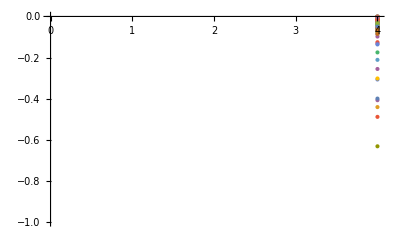

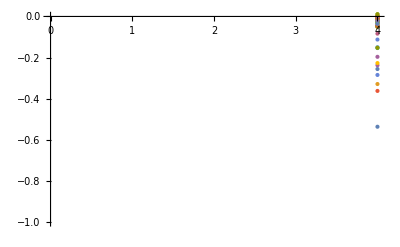

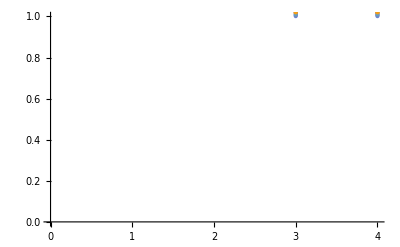

```mathematica
ListPlot[Table[phystest[[i,1]],{i,1,Length[cm]}],PlotRange->{-1,0}]

ListPlot[Table[phystest[[i,2]],{i,1,Length[cm]}],PlotRange->{-1,0}]
ListPlot[Table[phystest[[i,3]],{i,1,Length[cm]}],PlotRange->{0,1}]
```

```mathematica
Clear[cm]
```

```mathematica
Eigenvalues[σ[a,b,cp,cm]]//FullSimplify
```

{1/2 (a+b-√((a-b)^2+4 cm^2)),1/2 (a+b+√((a-b)^2+4 cm^2)),1/2 (a+b-√((a-b)^2+4 cp^2)),1/2 (a+b+√((a-b)^2+4 cp^2))}

```mathematica
Eigenvalues[σ[a,b,cp,cm]+ⅈ Σ]//FullSimplify
```

{1/2 (a+b-√((a-b)^2+2 (2+cm^2+cp^2-√(4 (a-b)^2+(4+(cm-cp)^2) (cm+cp)^2)))),1/2 (a+b+√((a-b)^2+2 (2+cm^2+cp^2-√(4 (a-b)^2+(4+(cm-cp)^2) (cm+cp)^2)))),1/2 (a+b-√((a-b)^2+2 (2+cm^2+cp^2+√(4 (a-b)^2+(4+(cm-cp)^2) (cm+cp)^2)))),1/2 (a+b+√((a-b)^2+2 (2+cm^2+cp^2+√(4 (a-b)^2+(4+(cm-cp)^2) (cm+cp)^2))))}

```mathematica
Eigenvalues[ⅈ Σ . σ[a,b,cp,cm]]//FullSimplify
```

{-(ⅈ √(-a^2-b^2-2 cm cp-√(a^4+b^4+4 b^2 cm cp-2 a^2 (b^2-2 cm cp)+4 a b (cm^2+cp^2))))/(√2),(ⅈ √(-a^2-b^2-2 cm cp-√(a^4+b^4+4 b^2 cm cp-2 a^2 (b^2-2 cm cp)+4 a b (cm^2+cp^2))))/(√2),-(ⅈ √(-a^2-b^2-2 cm cp+√(a^4+b^4+4 b^2 cm cp-2 a^2 (b^2-2 cm cp)+4 a b (cm^2+cp^2))))/(√2),(ⅈ √(-a^2-b^2-2 cm cp+√(a^4+b^4+4 b^2 cm cp-2 a^2 (b^2-2 cm cp)+4 a b (cm^2+cp^2))))/(√2)}